## 1. Гистограмма.

```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\Studies\2 kurs\Neutral Networks\NG4P02 GolubovichRoman

```mathematica
ClearAll[LoadMNIST];
LoadMNIST[SetName_String]:=Module[{F,FDummy,Counter,Rows,Cols,Digits,Images},
F=OpenRead[ToLowerCase[SetName]<>"-images.idx3-ubyte",BinaryFormat->True];
{FDummy,Counter,Rows,Cols}=BinaryRead[F,Array["Integer32"&,4],ByteOrdering->+1];
Images=Partition[BinaryReadList[F,"Byte",ByteOrdering->+1],Rows Cols];
Close[F];
F=OpenRead[ToLowerCase[SetName]<>"-labels.idx1-ubyte",BinaryFormat->True];
{FDummy,Counter}=BinaryRead[F,Array["Integer32"&,2],ByteOrdering->+1];
Digits=BinaryReadList[F,"Byte",ByteOrdering->+1];
Close[F];
{Digits,Images}]
```

```mathematica
Map[Dimensions,Train=LoadMNIST["train"]];
```

```mathematica
Map[Dimensions,Test=LoadMNIST["t10k"]];
```

```mathematica
DynamicModule[{m=4},Grid[{{Row@{"Magnification: ",SetterBar[Dynamic@m,Range[10]]},SpanFromLeft},{Manipulate[Style[Train⟦1,n⟧,Bold,24+2 m]->Image[256-Partition[Train[[2,n]],28],"Byte",ColorSpace->"GrayScale",Magnification->m],{{n,1,"Train"},1,Length@Train⟦2⟧,1,Appearance->"Labeled"},Paneled->False],Manipulate[Style[Test⟦1,n⟧,Bold,24+2 m]->Image[256-Partition[Test[[2,n]],28],"Byte",ColorSpace->"GrayScale",Magnification->m],{{n,1,"Test"},1,Length@Test⟦2⟧,1,Appearance->"Labeled"},Paneled->False]}},Frame->All,FrameStyle->Gray]];
```

```mathematica
pos6= Flatten@Position[Test[[1]],6];
```

```mathematica
posnot6 = Complement[Range[10000],pos6];
```

```mathematica
Test6 =Partition[Test[[2]][[#]],28]&/@pos6;
```

```mathematica
Testnot6 =Partition[Test[[2]][[#]],28]&/@posnot6;
```

```mathematica
rowcolhist6= Table[Test6[[All, row,col]],{row,1,28},{col,1,28}];
```

```mathematica
rowcolhistnot6= Table[Testnot6[[All, row,col]],{row,1,28},{col,1,28}];
```

```mathematica
Manipulate[Histogram[{Style[rowcolhist6[[i,j]],Blue],Style[rowcolhistnot6[[i,j]],Red]},35],{{i,10,"Row"},1,28,1},{{j,21,"Col"},1,28,1},ControlType->Setter]
```

Part::partd: Part specification rowcolhist6⟦10,21⟧ is longer than depth of object.

Part::partd: Part specification rowcolhistnot6⟦10,21⟧ is longer than depth of object.

Part::partd: Part specification rowcolhist6⟦10,21⟧ is longer than depth of object.

Part::partd: Part specification rowcolhistnot6⟦10,21⟧ is longer than depth of object.

## 2. Нормально распределённая случайная величина.

```mathematica
body[i_,j_]:={{Style[rowcolhist6[[i,j]],Blue],Style[rowcolhistnot6[[i,j]],Red]},
{Style[Total@rowcolhist6[[i]],Blue],Style[Total@rowcolhistnot6[[i]],Red]},
{Style[Total@rowcolhist6[[All,j]],Blue],Style[Total@rowcolhistnot6[[All,j]],Red]},
{Style[Total@rowcolhist6[[All,j]] + Total@rowcolhist6[[i]]-rowcolhist6[[i, j]],Blue],Style[Total@rowcolhistnot6[[All,j]] + Total@rowcolhistnot6[[i]]-rowcolhistnot6[[i, j]],Red]}};
```

```mathematica
Manipulate[Manipulate[Histogram[body[i,j][[k]],35],{{i,10,"Row"},1,28,1},{{j,21,"Col"},1,28,1},ControlType->Setter],{k,{1,2,3,4}}]
```

Histogram::ldata: 21 is not a valid dataset or list of datasets.

## 3. Функция плотности вероятности.

```mathematica
words = {"Пиксель","Строка","Столбец","Крест"};
```

```mathematica
body2[i_:10,j_:21]:={{rowcolhist6[[i]][[j]],rowcolhistnot6[[i]][[j]]},
{Total@rowcolhist6[[i]],Total@rowcolhistnot6[[i]]},
{Total@rowcolhist6[[All,j]],Total@rowcolhistnot6[[All, j]]},
{Total@rowcolhist6[[All, j]] + Total@rowcolhist6[[i]]-rowcolhist6[[i]][[j]],Total@rowcolhistnot6[[All, j]] + Total@rowcolhistnot6[[i]]-rowcolhistnot6[[i]][[j]]}};
```

```mathematica
muSigma = Join[{{"μ","σ"}},Flatten[Table[{N@Mean[body2[][[i,j]]],N@StandardDeviation[body2[][[i,j]]]},{i,1,4},{j,1,2}],1]]
```

{{μ,σ},{9.70564,41.4882},{81.5364,105.771},{842.82,317.081},{1515.24,863.906},{1274.33,657.766},{991.719,943.174},{2107.44,833.597},{2425.42,1407.75}}

```mathematica
friendFoe = Join[{{"",SpanFromLeft}},{{"Пиксель","Свой"},{SpanFromAbove,"Чужой"},{"Строка","Свой"},{SpanFromAbove,"Чужой"},{"Столбец","Свой"},{SpanFromAbove,"Чужой"},{"Крест","Свой"},{SpanFromAbove,"Чужой"}}];
```

```mathematica
Grid[Join[friendFoe,muSigma,2],Frame->All,Background->{{1->LightGray},{{{LightRed,LightBlue}},1->LightGray}}]
```

|  | μ | σ
Пиксель | Свой | 9.70564 | 41.4882
 | Чужой | 81.5364 | 105.771
Строка | Свой | 842.82 | 317.081
 | Чужой | 1515.24 | 863.906
Столбец | Свой | 1274.33 | 657.766
 | Чужой | 991.719 | 943.174
Крест | Свой | 2107.44 | 833.597
 | Чужой | 2425.42 | 1407.75

```mathematica
man[k_]:=Show[Histogram[body[10,21][[k]],35,"PDF"],Plot[{PDF[NormalDistribution@@muSigma[[2;;]][[2k-1]],x],PDF[NormalDistribution@@muSigma[[2;;]][[2k]],x]},{x,0,10000},PlotStyle->{Blue,Red}]]
```

```mathematica
TabView[{"Пиксель"->#@1,"Строка"->#@2,"Столбец"->#@3,"Крест"->#@4}&@man]
```

1234

## 4. Качество входных параметров.

```mathematica
rowmeans = {Table[Mean[Total@Test6[[All,i]]],{i,1,28}],Table[Mean[Total@Testnot6[[All,i]]],{i,1,28}]};
```

```mathematica
colmeans = {Table[Mean[Total@Test6[[All,All, i]]],{i,1,28}],Table[Mean[Total@Testnot6[[All,All,i]]],{i,1,28}]};
```

```mathematica
crossmeans = {Table[Mean[Total[Test6[[All,i]],{2}] + Total[Test6[[All,All,j]],{2}] - Test6[[All,i,j]]],{i,1,28},{j,1,28}],Table[Mean[Total[Testnot6[[All,i]],{2}] + Total[Testnot6[[All,All,j]],{2}] - Testnot6[[All,i,j]]],{i,1,28},{j,1,28}]};
```

```mathematica
rowdivs = {Table[StandardDeviation[Total@Test6[[All,i]]],{i,1,28}],Table[StandardDeviation[Total@Testnot6[[All,i]]],{i,1,28}]};
```

```mathematica
coldivs = {Table[StandardDeviation[Total@Test6[[All,i]]],{i,1,28}],Table[StandardDeviation[Total@Testnot6[[All,i]]],{i,1,28}]};
```

```mathematica
crossdivs = {Table[StandardDeviation[Total[Test6[[All,i]],{2}] + Total[Test6[[All,All,j]],{2}] - Test6[[All,i,j]]],{i,1,28},{j,1,28}],Table[StandardDeviation[Total[Testnot6[[All,i]],{2}] + Total[Testnot6[[All,All,j]],{2}] - Testnot6[[All,i,j]]],{i,1,28},{j,1,28}]};
```

```mathematica
q[mean_, div_]:=If[#==0,0,N@(Abs[mean[[1]]-mean[[2]]]/#)]&@(Plus@@div)
```

```mathematica
Feature[row_]:=With[{res=ConstantArray[0,784], ind=Transpose[{Range[28(row-1)+1, 28 *row]}]},ReplacePart[res,ind->1]]
```

```mathematica
Feature[Null,col_]:=With[{res=ConstantArray[0,784], ind=Transpose[{Range[col,col+28*27,28]}]},ReplacePart[res,ind->1]]
```

```mathematica
Feature[row_,col_]:=With[{res=ConstantArray[0,784],ind1=Transpose[{Range[28(row-1)+1, 28 *row]}],ind2=Transpose[{Range[col,col+28*27,28]}]},ReplacePart[res,Join[ind1,ind2]->1]]
```

```mathematica
qs = Flatten[Table[q[crossmeans[[All,i,j]], crossdivs[[All,i,j]]],{i,1,28},{j,1,28}]];
```

```mathematica
largeqs = TakeLargest[qs,30];
```

```mathematica
largepos = Position[qs,#]&/@largeqs//Flatten;
```

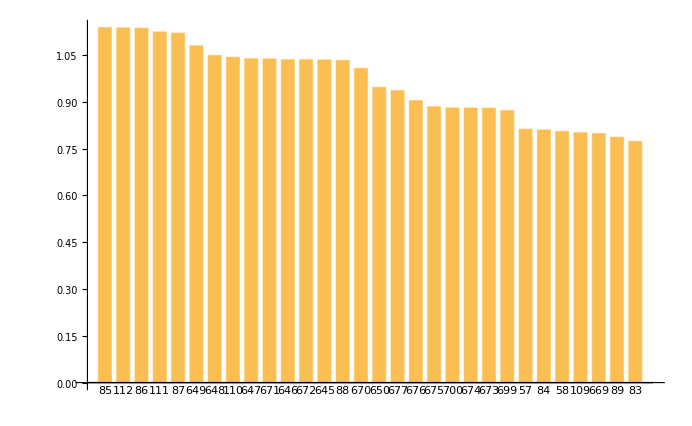

```mathematica
BarChart[largeqs,ChartLabels->largepos]
```

## 5. Стандартизация входных параметров.

```mathematica
Dimensions[wlayer1=Table[Feature[Ceiling[i/28],Mod[i,28,1]],{i,largepos}]]
```

{30,784}

```mathematica
firstlayer[W1_]:=Standardize@N[W1.#]&
```

```mathematica
firstlayer[wlayer1][Flatten[Test6[[1]]]]
```

{1.50185,1.50185,1.50185,1.50185,1.50185,-0.64365,-0.64365,1.50185,-0.64365,-0.64365,-0.64365,-0.64365,-0.64365,1.50185,-0.64365,-0.64365,-0.64365,-0.64365,-0.64365,-0.64365,-0.64365,-0.64365,-0.64365,-0.64365,-0.64365,-0.64365,1.50185,-0.64365,1.50185,-0.64365}

## 6. Распознавание Свой/Чужой.

```mathematica
W[μσfriend_,μσfoe_]:=(μσfriend⟦1⟧-μσfoe⟦1⟧)/(μσfriend⟦2⟧*μσfoe⟦2⟧)
```

```mathematica
wlayer2 =Flatten[Table[N@W[crossmeans[[All,i,j]], crossdivs[[All,i,j]]],{i,1,28},{j,1,28}]][[#]]&/@largepos;
```

```mathematica
AppendTo[wlayer2,w0];
```

```mathematica
secondlayer[W2_]:=N[(Most[W2].# + Last[W2])&]
```

```mathematica
secondlayer[wlayer2][firstlayer[wlayer1][Flatten[Test6[[1]]]]]
```

0.322432+w0

```mathematica
qs//Dimensions
```

{784}

```mathematica
NBC[x_]:=secondlayer[wlayer2][firstlayer[wlayer1][x]]
```

```mathematica
NBC[Flatten[Test6[[1]]]]
```

0.322432+w0

```mathematica
w0 = Values[Solve[Mean[NBC[#]&/@(Flatten[#]&/@Testnot6)]==0,w0]][[1]][[1]]
```

0.115262

```mathematica
UnitStep[NBC[Flatten[Test6[[1]]]]]
```

1

```mathematica
Export["NG4P02 GolubovichRoman.xlsx", {"Layer"->wlayer2}]
```

NG4P02 GolubovichRoman.xlsx

## 7. Ошибки 1-го и 2-го рода.

```mathematica
pos6train= Flatten@Position[Train[[1]],6];
```

```mathematica
posnot6train = Complement[Range[60000],pos6train];
```

```mathematica
Train6 =Train[[2]][[#]]&/@pos6train;
```

```mathematica
Trainnot6 =Train[[2]][[#]]&/@posnot6train;
```

### 1 род

```mathematica
Friend=UnitStep[NBC[#]]&/@Train6;
```

```mathematica
resFriendIsFoe = Count[Friend,0]
```

14

```mathematica
N@((100*resFriendIsFoe)/(Length@Friend))
```

0.236566

### 2 род

```mathematica
Foe = UnitStep[NBC[#]]&/@Trainnot6;
```

Standardize::scl: The scale function StandardDeviation evaluated to a list or zero.

General::stop: Further output of Standardize::scl will be suppressed during this calculation.

```mathematica
resFoeIsFriend = Count[Foe,1]
```

24096

```mathematica
N@((100*resFoeIsFriend)/(Length@Foe))
```

44.5546